## Brian — PS 10 — 2025-02-25 — Solution

## EIWL3 Sections 26, 27, and 28

## Exercises from EIWL3 Section 26

```mathematica
(* 26.1 *) Power[#,2]&/@Range[20]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
(* 26.2 *) Blend[{Red,#}]&/@{Yellow,Green,Blue}
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

```mathematica
(* 26.3 *) Framed[Column[{ToUpperCase[#],#}]]&/@Alphabet[]
```

{A
a,B
b,C
c,D
d,E
e,F
f,G
g,H
h,I
i,J
j,K
k,L
l,M
m,N
n,O
o,P
p,Q
q,R
r,S
s,T
t,U
u,V
v,W
w,X
x,Y
y,Z
z}

```mathematica
(* 26.4 *)Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}






France | -Graphics-
Germany | -Graphics-
Japan | -Graphics-
United Kingdom | -Graphics-
United States | -Graphics-

```mathematica
(* 26.5 *) {EntityValue[#,"Name"],EntityValue[#,"Flag"]}&/@EntityList[EntityClass["Country","GroupOf5"]]//Grid[#,Frame->All]&
```

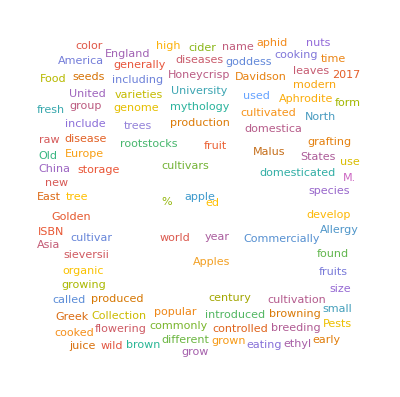
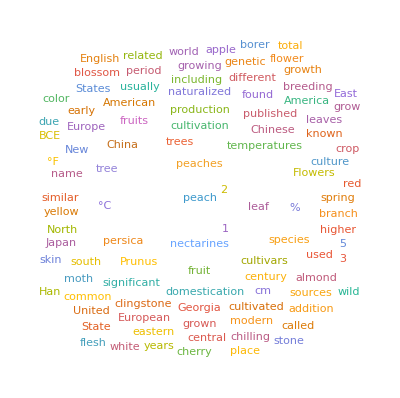
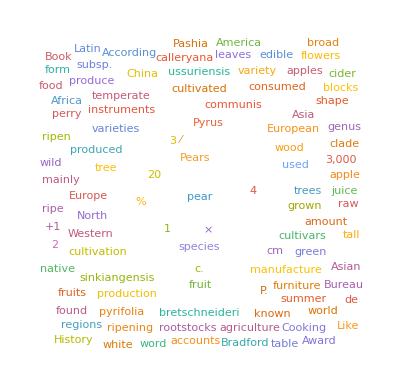

```mathematica
(* 26.6 *) WordCloud[WikipediaData[#]]&/@{"apple","peach","pear"}
```

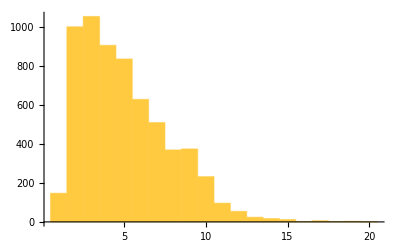
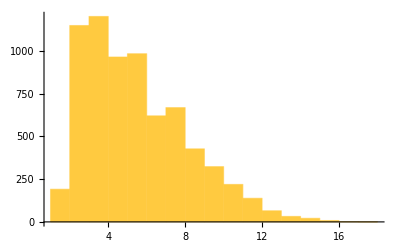
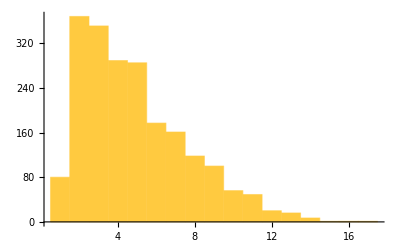

```mathematica
(* 26.7 *) Histogram[StringLength[TextWords[WikipediaData[#]]]]&/@{"apple","peach","pear"}
```

```mathematica
(* 26.8 *)GeoListPlot[#,GeoRange->EntityClass["Country","CentralAmerica"]]&/@EntityList[ EntityClass["Country","CentralAmerica"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Exercises from EIWL3 Section 27

```mathematica
(* 27.1 *) NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 27.2 *) NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
(* 27.3 *) NestList[
Rotate[Framed[#],RandomReal[]360°]&,
Style["A",50],
5
]
(* This was another one that I used indentation to help me *)
(* see the organization of the functions and their arguments. *)
```

{A,A,A,A,A,A}

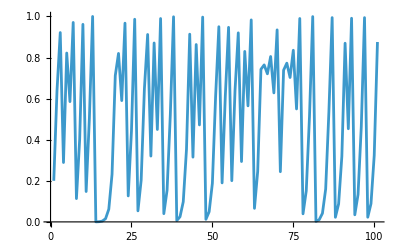

```mathematica
(* 27.4 *) ListLinePlot[NestList[ 4#(1-#)&,0.2,100]]
```

```mathematica
(* 27.5 *) Nest[1+1/#&,1,30]//N
```

1.61803

```mathematica
(* 27.6 *) NestList[3#&,1,10] (* This gives 11 results, of course. *)
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

```mathematica
(* 27.7 *) NestList[(#+2/#)/2&,1.0,5]-Sqrt[2]
```

{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}

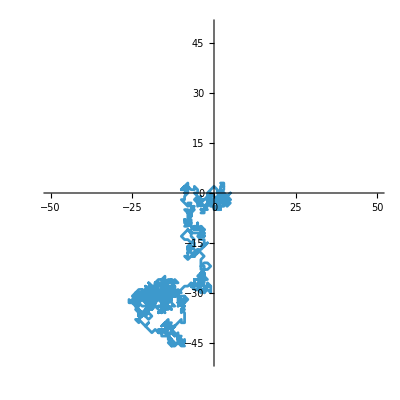

```mathematica
(* 27.8 *) (* Hmmm. He asked for a Graphics. Is it ok that I used a ListLinePlot? *)
(* I used AspectRatio->1 and PlotRange->{{-50,50},{-50,50}} so that the result *)(* wouldn't be scrunched along whichever axis happened the walk went further. *)
ListLinePlot[NestList[#+{RandomChoice[{+1,0,-1}],RandomChoice[{+1,0,-1}]}&,{0,0},1000],AspectRatio->1,PlotRange->{{-50,50},{-50,50}}]
```

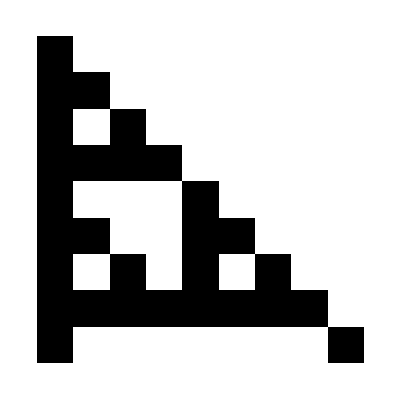

```mathematica
(* 27.9 *) NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},8]//ArrayPlot
```

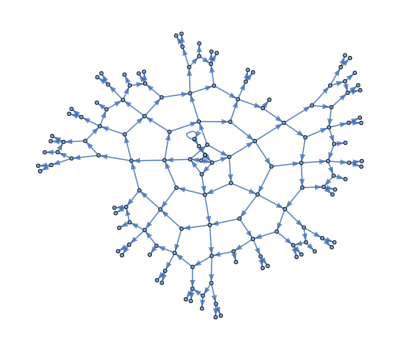

```mathematica
(* 27.10 *) NestGraph[{#+1,2#}&,0,10]
```

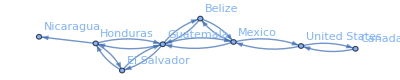

```mathematica
(* 27.11 *) NestGraph[#["BorderingCountries"]&,,4,VertexLabels->All]
```

## Exercises from EIWL3 Section 28

```mathematica
(* 28.1 *) 123^321>456^123
```

True

```mathematica
Total[IntegerDigits[#]]<5&/@3
```

3

```mathematica
Select[IntegerDigits[#]=={1,2},Range[100]]
```

True

```mathematica
(* 28.2 *) Select[
Range[100],
Total[IntegerDigits[#]]<5&
]
```

{1,2,3,4,10,11,12,13,20,21,22,30,31,40,100}

```mathematica
(* 28.3 *) If[PrimeQ[#],Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
(* 28.4 *) Select[
WordList[],First[Characters[#]]=="p" && Last[Characters[#]]=="p" &
]
```

{pap,paperclip,parsnip,partisanship,partnership,pawnshop,peep,penmanship,pep,pickup,pileup,pip,plop,plump,polyp,pomp,pop,premiership,prep,primp,professorship,prop,proprietorship,pulp,pump,pup}

```mathematica
(* 28.5 *) Select[Prime[Range[100]],Last[IntegerDigits[#]]==3&]
```

{3,13,23,43,53,73,83,103,113,163,173,193,223,233,263,283,293,313,353,373,383,433,443,463,503,523}

```mathematica
(* 28.6 *) Select[RomanNumeral[Range[100]],!StringContainsQ[#,"I"]&]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

```mathematica
(* 28.7 *) Select[RomanNumeral[Range[1000]],#==StringReverse[#]&]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

```mathematica
(* 28.8 *) Select[IntegerName[Range[100]],First[Characters[#]]==Last[Characters[#]]&]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

```mathematica
(* 28.9 *) Select[TextWords[WikipediaData["words"]],StringLength[#]>15&]
```

{yibi-jarran-gabun,yibi-gabun-jarran,orthographically,multiple-morpheme,Proto-Indo-European,978-0-08-044854-1}

```mathematica
(* 28.10 *) NestList[If[EvenQ[#],#/2,3#+1]&,1000,200]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

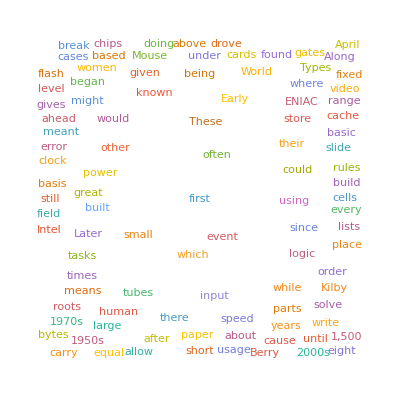

```mathematica
(* 28.11 *) WordCloud[Select[TextWords[WikipediaData["computers"]],StringLength[#]==5&]]
```

```mathematica
(* 28.12 *) Select[WordList[],StringLength[#]>=3&&Take[Characters[#],3]==Take[Characters[StringReverse[#]],3]&& #!=StringReverse[#]&]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

```mathematica
(* 28.13 *) Select[WordList[],Total[LetterNumber[Characters[#]]]==100&]
```

{acclimation,accumulate,acknowledge,acquitted,adulthood,affectation,alienation,amiableness,analysis,annually,answerable,anterior,apoplectic,appertain,appointed,apropos,aquamarine,archdiocesan,asbestos,attitude,autoclave,automated,avocation,awfully,beetroot,benediction,bettering,bewitching,bipartite,birthmark,blissful,botanist,bouillon,boulevard,boundary,boycott,breviary,bronchus,browser,burnished,cacophony,candidature,cardiograph,carouser,carpenter,carroty,censurable,ceramicist,chastening,chimpanzee,chromium,clinically,clockwise,clotting,coatroom,collecting,cometary,companion,comport,concavely,condensate,confabulate,congenital,congress,conjoint,conjugated,conjunct,connivance,contented,cookout,corridor,costumed,couchette,coverlet,coyness,creosote,crudity,culture,curettage,cutout,cysteine,debarkation,declarative,declension,decorous,deliquesce,delivery,demobilize,demodulate,denominate,depletion,dewberry,diagonally,digestive,dinginess,disarranged,discernible,discipline,discommode,discredited,disjoint,dispraise,distrait,divinely,dooryard,doubleheader,drizzle,dumbfound,duologue,ebullient,egoistical,elsewhere,emasculate,embodiment,emendation,empathetic,encrust,epitaxy,espouse,eulogize,eventual,excellent,excoriate,falseness,fatalistic,fatherhood,ferryman,finitely,fluorine,flurry,forefoot,forewarn,forgiver,forsaking,fountain,frisson,gauntlet,geographer,gladiolus,glissando,glutamate,godparent,grandaunt,grappling,grouper,grumpy,harmonics,healthily,hemoglobin,hirsute,hobbyist,hollering,holograph,honeycomb,honoring,hospital,hotness,imbroglio,immature,impaction,imported,impotence,inadequacy,inapplicable,inefficient,inflation,ingrown,innately,innovate,inoculate,insecticide,intellect,interbreed,interfere,irritate,jailhouse,judiciary,kibitzer,knothole,landholding,landscaping,largeness,leveraging,liberalism,liberator,lightning,likelihood,limpidly,litotes,lubricant,macrocosm,magnetize,martinet,martingale,matchless,matchmaking,maximize,meatpacking,mercantile,mercurial,merganser,meridional,merrily,midpoint,mirrored,misdirect,missus,molecular,morphemic,moussaka,mummify,nastily,neoclassic,nestling,neuronal,nihilist,ninepins,nonhuman,nostalgic,notional,numeracy,nutty,obscenely,offhandedly,operetta,ornament,outflank,outlier,outlined,outrank,outset,overboard,palpitate,paramecium,pasture,pathless,personage,personal,perturb,phagocyte,phlebitis,pianistic,pilaster,pistachio,plastered,plebiscite,plummet,plummy,postdate,posting,postpaid,potbellied,pounding,pouring,prevent,primary,printer,producer,profuse,progeny,publicly,pumpkin,pursue,putter,pyridine,quadrangle,quarry,quarter,quicklime,radiocarbon,raillery,ravisher,receptor,reciprocal,redeploy,refinery,reflation,regimented,regroup,reimpose,renovate,repress,reprint,reprobate,reputable,reschedule,researcher,reshuffle,resolved,restore,retiring,reversal,riverbank,roadster,roomful,roommate,ruction,sagebrush,saintlike,saintly,salacious,savory,scoreboard,scrapbook,scrummage,sculpted,scuttle,selective,self-defense,semaphore,semitone,septicemia,services,session,shadowing,shakedown,shakeout,shattered,shibboleth,shipyard,shooter,shortcake,shrieking,sightly,simulate,sleepyhead,smitten,snobbery,socialism,soughing,sparkler,spirited,splashy,spyhole,squint,stagecraft,stalemated,starfish,starling,status,strangled,stress,striker,subsume,sucrose,surcharge,surely,sweetened,sweptback,swimmer,swollen,syndicate,tailspin,telephone,telescope,temperance,temporal,tensely,tetanus,thalidomide,therefore,thickening,thievish,thirty,thorny,threatened,thumbnail,tinkerer,towards,traction,trademarked,transect,transom,trembling,triplet,tropics,truism,tularemia,tuppence,turkey,turnoff,twisted,unaltered,unavailable,unbounded,unbridgeable,unbroken,uncombined,underdone,underlay,undress,unequaled,unfasten,unfreeze,unhorse,unkempt,unlighted,unmanly,unmatchable,unmodified,unrelated,unwearied,urbanized,urticaria,useless,utensil,variety,varnished,venation,verbalize,vinous,vouchsafe,waterbird,Wednesday,whenever,whirling,whiskey,wholesale,whooper,writing,yarrow}